```mathematica
sigma = 0.6;
W = 16000;
d[v_] := 0.01 * sigma * v ^ 2 + 0.95 / sigma * (W/v)^2
```

```mathematica
d[10]
```

4.05333×10^6

```mathematica
d'
```

-(8.10667×10^8)/#1^3+0.012 #1&

```mathematica
d'[10]
```

-810667.

```mathematica
DSolve[d'[v]==0, d[v], v]
```

DSolve::dsfun: (4.05333×10^8)/v^2+0.006 v^2 cannot be used as a function.

DSolve[-(8.10667×10^8)/v^3+0.012 v==0,(4.05333×10^8)/v^2+0.006 v^2,v]

```mathematica
DSolve[d']
```

DSolve::argmu: DSolve called with 1 argument; 3 or more arguments are expected.

DSolve[-(8.10667×10^8)/#1^3+0.012 #1&]

```mathematica
d'
```

-(8.10667×10^8)/#1^3+0.012 #1&

```mathematica
D[d[v], v]
```

-(8.10667×10^8)/v^3+0.012 v

```mathematica
g:=D[d[v], v]
```

```mathematica
NSolve[g[v]==0, v]
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{{v→InverseFunction[-(8.10667×10^8)/v^3+0.012 v,1,1][0.]}}

```mathematica
DSolve[g[v], d[v], v]
```

DSolve::dsfun: (4.05333×10^8)/v^2+0.006 v^2 cannot be used as a function.

DSolve[(-(8.10667×10^8)/v^3+0.012 v)[v],(4.05333×10^8)/v^2+0.006 v^2,v]

```mathematica
d[v]
```

(4.05333×10^8)/v^2+0.006 v^2

```mathematica
DSolve[g[v]==0, v]
```

DSolve::argm: DSolve called with 2 arguments; 3 or more arguments are expected.

DSolve[(-(8.10667×10^8)/v^3+0.012 v)[v]==0,v]

```mathematica
DSolve[g[v]==0, d[v],v]
```

DSolve::dsfun: (4.05333×10^8)/v^2+0.006 v^2 cannot be used as a function.

DSolve[(-(8.10667×10^8)/v^3+0.012 v)[v]==0,(4.05333×10^8)/v^2+0.006 v^2,v]

```mathematica
NSolve[g[v]==0, v]
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{{v→InverseFunction[-(8.10667×10^8)/v^3+0.012 v,1,1][0.]}}

```mathematica
NSolve[g[v]0, v]
```

{{}}

```mathematica
NSolve[g[v]=
0, v]
```

Set::write: Tag Plus in (-(8.10667×10^8)/v^3+0.012 v)[v] is Protected.

{{}}

```mathematica
NSolve[g[v]==0, v]
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{{v→InverseFunction[-(8.10667×10^8)/v^3+0.012 v,1,1][0.]}}

```mathematica
s = NSolve[g==0, v, Reals]
```

{{v→509.818},{v→-509.818}}

```mathematica
s[0]
```

{{v→509.818},{v→-509.818}}[0]

```mathematica
v1 = 509.8181203738957;
v2 = -509.8181203738958;
```

```mathematica
d[v1]
```

3118.97

```mathematica
d[v2-10]
```

```mathematica
3121.3282423926994
```

3121.33

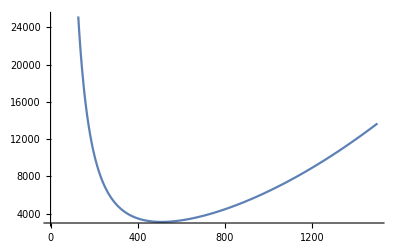

```mathematica
Plot[d[v], {v, 0, 1500}]
```

```mathematica
Manipulate[Plot[0.01 * sigma * v^ 2 + 0.95 / sigma * (w/v)^2, {v, 0, 1500}], {w, 12000, 20000, 10}]
```

```mathematica
W=12000;
sigma = 0.6;
While[W<20000,
d[v_] := 0.01 * sigma * v ^ 2 + 0.95 / sigma * (W/v)^2;
g:=D[d[v], v];
W = W + 100;
s = NSolve[g==0, v, Reals];
t = v/.s[[1]] ;
If[t>0.0, 
Print[t],
Print[v/.s[[2]]]
];
]
```

443.351

445.18

447.

448.814

450.62

452.419

454.21

455.995

457.773

459.544

461.308

463.065

464.816

466.56

468.298

470.029

471.754

473.473

475.185

476.891

478.591

480.285

481.974

483.656

485.332

487.003

488.668

490.327

491.981

493.629

495.272

496.909

498.541

500.168

501.789

503.405

505.016

506.622

508.222

509.818

511.409

512.995

514.575

516.152

517.723

519.289

520.851

522.408

523.961

525.508

527.052

528.591

530.125

531.655

533.181

534.702

536.219

537.731

539.24

540.744

542.244

543.74

545.231

546.719

548.203

549.682

551.158

552.63

554.097

555.561

557.022

558.478

559.93

561.379

562.824

564.265

565.703

567.137

568.567

569.994

```mathematica
l = {}
```

{}

```mathematica
AppendTo[l, 16]
```

{16}

```mathematica
l
```

{16}